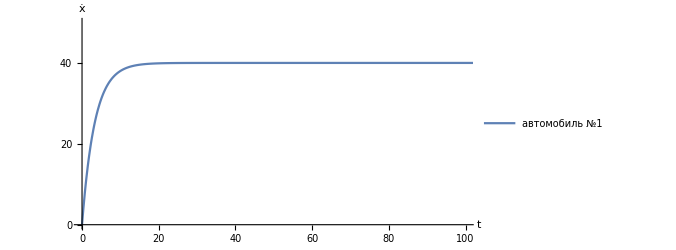

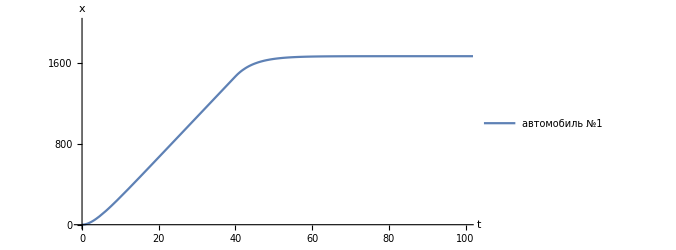

speed.pdf

path.pdf

```mathematica
speed =Module[{e},
tt=150;
tmax =150;
Subscript[V, max] =40;
vm=0;

R[t_] := If[t <= tt, 1,0];
RR[t_] := If[t <= tt, 0,1];
λ=0;
a =0.3;
q=0.2;

Module[{solF, solS, solT, u,  v,  w},

solF= NDSolve[{u''[t]== R[t]*a*(Subscript[V, max]-u'[t])+RR[t]*q*(vm-u'[t]), u[t /; t≤ 0] == -0*λ, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];
ParametricPlot[{Evaluate[{t,u'[t]} /. solF]},{t,0,tmax}, PlotRange->{{0,100},{0,50}},AxesLabel->{Style[t,15],Style[ẋ,15]},FormatType->StandardForm,PlotLegends->Placed[{"автомобиль №1","автомобиль №2","автомобиль №3","автомобиль №4","автомобиль №5"},{Right,Center}],ImageSize->500,Ticks->{{0,20,40,60,80,100},{0,10,20,30,40,50,60}},
TicksStyle->Directive[Automatic,15]]]]
path =Module[{e},
tt=150;
tmax =150;
Subscript[V, max] =40;
vm=0;

R[t_] := If[t <= tt, 1,0];
RR[t_] := If[t <= tt, 0,1];

λ=0;
a =0.3;
q=0.2;

Module[{solF, solS, solT, u,  v,  w},

solF= NDSolve[{u''[t]== R[t]*a*(Subscript[V, max]-u'[t])+(1-R[t])*q*(vm-u'[t]), u[t /; t≤ 0] == -0*λ, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];
ParametricPlot[{Evaluate[{t,u[t]/40} /. solF]},{t,0,tmax}, PlotRange->{{0,100},{0,50}},AxesLabel->{Style[t,15],Style[x,15]},FormatType->StandardForm,PlotLegends->Placed[{"автомобиль №1","автомобиль №2","автомобиль №3","автомобиль №4","автомобиль №5"},{Right,Center}],ImageSize->500,Ticks->{{0,20,40,60,80,100},{{0,0},{10,400},{20,800},{30,1200},{40,1600},{50,2000},{60,2400},{80,3200},{100,4000}}},TicksStyle->Directive[Automatic,15]]]
]
Export["speed.pdf",speed]

Export["path.pdf",path]
```